```mathematica
<<MeshIO`
```

```mathematica
<<Render`
```

```mathematica
<<MeshOptimizePN`
```

### input and result

```mathematica
modelDir="C:\\Users\\charlesdu\\Documents\\research\\Weber14\\SOP_Code\\Alon_results\\shor_failed_Hanxiao";
```

```mathematica
filename="hand_3_i_H";
```

```mathematica
infile=FileNameJoin[{modelDir,filename<>".obj"}]
```

C:\Users\charlesdu\Documents\research\Weber14\SOP_Code\Alon_results\shor_failed_Hanxiao\hand_3_i_H.obj

```mathematica
mesh=ImportMesh[infile];
meshData=Import[infile,"Table"];
vt=Select[meshData,Length[#]>0&&#⟦1⟧=="vt"&]⟦All,2;;⟧;
uvmesh={vt,mesh⟦2⟧};
```

rest mesh

```mathematica
MeshToMeshRegion[mesh]
```

```mathematica
render[mesh]
```

init uv mesh

```mathematica
render[uvmesh]
```

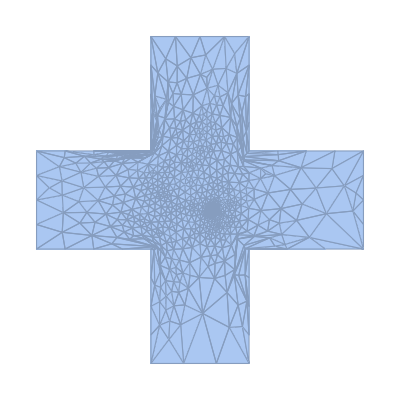

```mathematica
MeshToMeshRegion[uvmesh]
```

```mathematica
bndryVid=1+ImportString["3 4 6 491 496 502 492 7 179 1019 180 176 307 900 898 896 894 893 967 965 766 309 312 314 759 756 760 761 762 757 689 1001 708 572 782 777 713 566 573 494 495 1016 568 569 574 488","Table"]⟦1⟧
```

{4,5,7,492,497,503,493,8,180,1020,181,177,308,901,899,897,895,894,968,966,767,310,313,315,760,757,761,762,763,758,690,1002,709,573,783,778,714,567,574,495,496,1017,569,570,575,489}

```mathematica
B=1+ImportString[" 1  5  9 13 17 21 25 29 33 36 40 43","Table"]⟦1⟧;
```

```mathematica
B
```

{2,6,10,14,18,22,26,30,34,37,41,44}

```mathematica
ListPlot[MapThread[Labeled[#1,#2]&,{uvmesh⟦1,bndryVid⟧,bndryVid}],AspectRatio->1,Joined->True,PlotMarkers->"o"]
```

-Graphics-

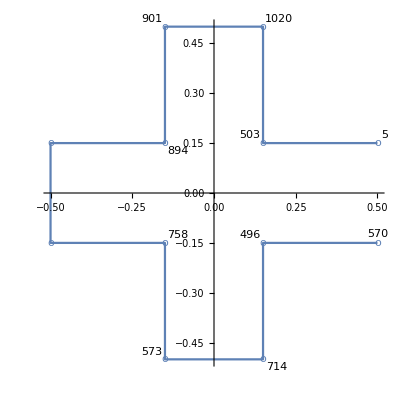

```mathematica
ListPlot[MapThread[Labeled[#1,#2]&,{uvmesh⟦1,bndryVid⟦B⟧⟧,bndryVid⟦B⟧}],AspectRatio->1,Joined->True,PlotMarkers->"o"]
```

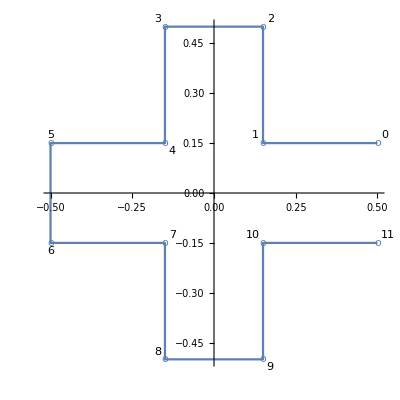

```mathematica
ListPlot[MapThread[Labeled[#1,#2]&,{uvmesh⟦1,bndryVid⟦B⟧⟧,Range[Length[B]]-1}],AspectRatio->1,Joined->True,PlotMarkers->"o"]
```

```mathematica
eF=1+ImportString["11  0  1
 1  2  3
 1  3  4
11  1  4
11  4  5
11  5  6
 7  8  9
 7  9 10","Table"]
```

{{12,1,2},{2,3,4},{2,4,5},{12,2,5},{12,5,6},{12,6,7},{8,9,10},{8,10,11}}

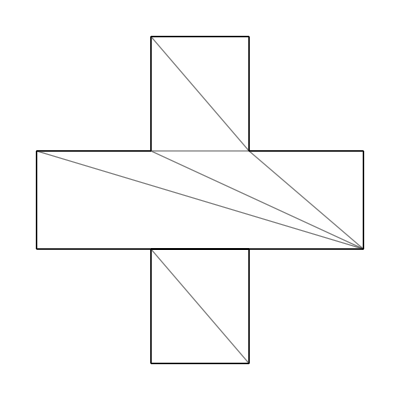

```mathematica
render[{uvmesh⟦1,bndryVid⟦B⟧⟧,eF}]
```

```mathematica
MeshToMeshRegion[{uvmesh⟦1,bndryVid⟦B⟧⟧,eF}]
```

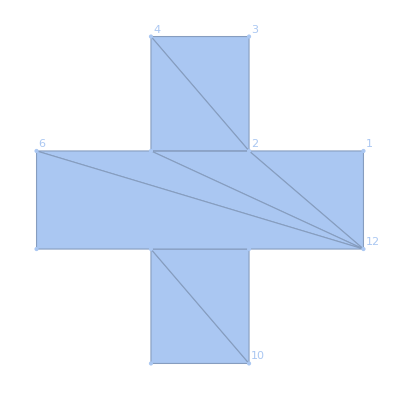

```mathematica
eF
```

{{12,1,2},{2,3,4},{2,4,5},{12,2,5},{12,5,6},{12,6,7},{8,9,10},{8,10,11}}

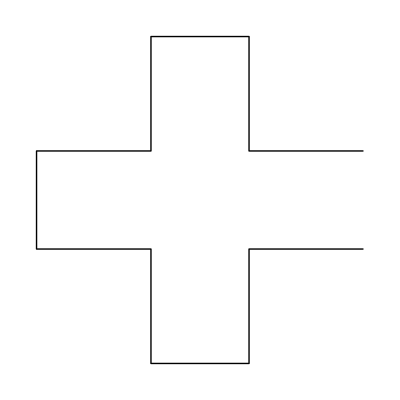

```mathematica
Graphics[Line@uvmesh⟦1,bndryVid⟦B⟧⟧]
```

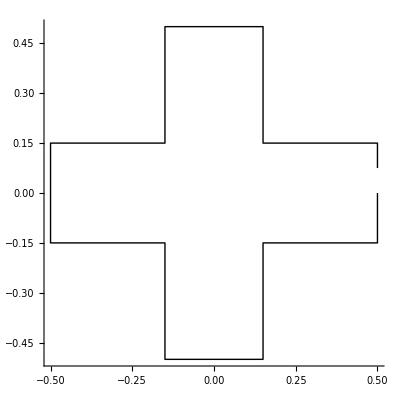

```mathematica
Graphics[Line[uvmesh⟦1,bndryVid⟧],Axes->True]
```

result mesh

```mathematica
(*res=Import["~/MEGAsync/winshare/bunny1-2k.mx"];*)
```

```mathematica
resMesh=ImportMesh["~/Downloads/research/weber14/models/grid2x2_L0.26_result.obj"];
```

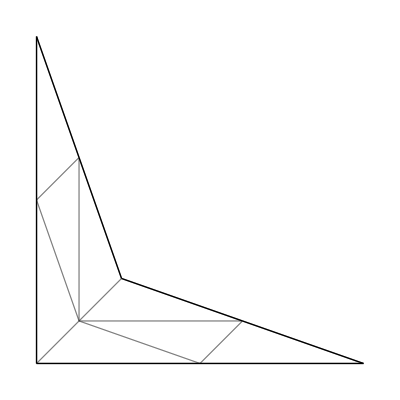

```mathematica
render[resMesh]
```

#### create input

```mathematica
{restmesh,initmesh,handles}=Import["~/OneDrive - Washington University in St. Louis/injective-mapping-data/mx/2D_ParamExamples/Tutte/bunny1-2k.mx"];
```

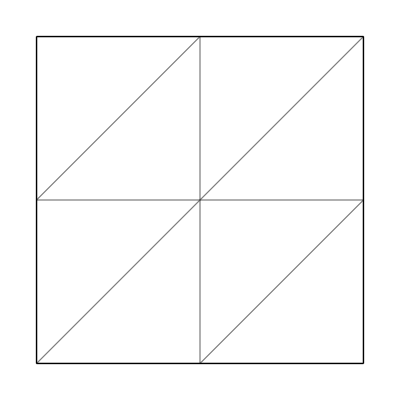

```mathematica
render[restmesh]
```

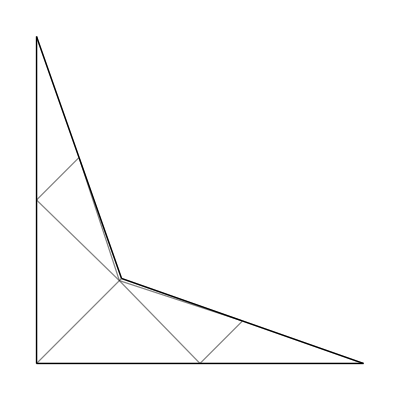

```mathematica
render[initmesh]
```

```mathematica
ExportMeshWithUV["~/Downloads/research/weber14/models/bunny1-2k-good.obj",restmesh,initmesh];
```

```mathematica
(*mesh=gridMesh[{2,2}];
mesh={N[mesh⟦1⟧],mesh⟦2⟧};*)
```

```mathematica
restmesh=mesh;
(*initmesh={N@tutteMesh⟦1⟧,tutteMesh⟦2⟧};*)
initmesh=res["resMesh"];
```